```mathematica
(*Definition of Clausen.*)Cl2[θ_]/;NumberQ[θ]:=Sum[Sin[k θ]/k^2,{k,1,1500}]//N
Derivative[1][Cl2][θ_]=-Log[2 Sin[θ/2]];

(*This series converges more fast.*)

Cl2[θ_]/;NumberQ[θ]:=θ (3-Log[Abs[θ] (1-θ^2/(4 Pi^2))])-2 Pi Log[(2 Pi+θ)/(2 Pi-θ)]+θ Sum[(Zeta[2 k]-1)/(k (2 k+1)) (θ/(2 Pi))^(2 k),{k,1,2}]//N

K[e_]/;NumberQ[e]:=Cl2[2 ArcCos[-(1/e)]]+ArcCos[-(1/e)] Log[-(2/e)+2 e]
(*-------------------------------------------------------------------------------------------------------------------------------------------------------*)
MS:=2 10^30
rel1:={et->4,ξ->1/105,c->3 10^8,G->6.674 10^-11,η->0.2,Ω->0.5}
rel:={et->4,ξ->1/50,c->3 10^8,G->6.674 10^-11,η->0.2,Ω->0.5}

(*-------------------------------------------------------------------------------------------------------------------------------------------------------*)
y=1/c^2;(*ξ=(G M)/(b c^2);*)
scale:= MS (3 10^8)^2 10^-3
fac:=8/5 G M^2 √y η^2 ξ^2 MS^2/scale
JFluxb:=13/(√(-1+et^2))+(2 et^2)/(√(-1+et^2))+(8/(-1+et^2)+(7 et^2)/(-1+et^2)) ArcCos[-1/et]+ξ (10391/(168 (-1+et^2))+(44753 et^2)/(336 (-1+et^2))+(50 et^4)/(7 (-1+et^2))-(925 η)/(18 (-1+et^2))-(4651 et^2 η)/(36 (-1+et^2))-(22 et^4 η)/(3 (-1+et^2))+(1105/(42 (-1+et^2)^(3/2))+(5749 et^2)/(42 (-1+et^2)^(3/2))+(13103 et^4)/(336 (-1+et^2)^(3/2))-(62 η)/(3 (-1+et^2)^(3/2))-(128 et^2 η)/((-1+et^2)^(3/2))-(157 et^4 η)/(4 (-1+et^2)^(3/2))) ArcCos[-1/et])+ξ^2 (7662413/(17010 (-1+et^2)^(3/2))+(11902151 et^2)/(19440 (-1+et^2)^(3/2))+(3472223 et^4)/(3360 (-1+et^2)^(3/2))+(4919 et^6)/(63 (-1+et^2)^(3/2))-(667207 η)/(2160 (-1+et^2)^(3/2))-(60527209 et^2 η)/(30240 (-1+et^2)^(3/2))-(18407141 et^4 η)/(10080 (-1+et^2)^(3/2))-(2474 et^6 η)/(21 (-1+et^2)^(3/2))+(2573 η^2)/(36 (-1+et^2)^(3/2))+(60791 et^2 η^2)/(72 (-1+et^2)^(3/2))+(6827 et^4 η^2)/(8 (-1+et^2)^(3/2))+(40 et^6 η^2)/((-1+et^2)^(3/2))+(20522/(81 (-1+et^2)^2)+(420545 et^2)/(756 (-1+et^2)^2)+(765025 et^4)/(756 (-1+et^2)^2)+(710887 et^6)/(2016 (-1+et^2)^2)-(33521 η)/(252 (-1+et^2)^2)-(8167 et^2 η)/(6 (-1+et^2)^2)-(496471 et^4 η)/(224 (-1+et^2)^2)-(365429 et^6 η)/(672 (-1+et^2)^2)+(65 η^2)/(3 (-1+et^2)^2)+(3137 et^2 η^2)/(6 (-1+et^2)^2)+(25025 et^4 η^2)/(24 (-1+et^2)^2)+(5327 et^6 η^2)/(24 (-1+et^2)^2)) ArcCos[-1/et])+ξ^3 (80656024399/(13970880 (-1+et^2)^2)+(125199835777 et^2)/(9313920 (-1+et^2)^2)+(481245953857 et^4)/(111767040 (-1+et^2)^2)+(52748500199 et^6)/(4967424 (-1+et^2)^2)+(1020617 et^8)/(1386 (-1+et^2)^2)-(101368790459 η)/(11430720 (-1+et^2)^2)-(516875125633 et^2 η)/(22861440 (-1+et^2)^2)-(4213346393 et^4 η)/(178605 (-1+et^2)^2)-(4200523433 et^6 η)/(169344 (-1+et^2)^2)-(553309 et^8 η)/(378 (-1+et^2)^2)+(345343 π^2 η)/(1920 (-1+et^2)^2)+(743453 et^2 π^2 η)/(3840 (-1+et^2)^2)-(7667 et^4 π^2 η)/(1920 (-1+et^2)^2)+(303706259 η^2)/(181440 (-1+et^2)^2)+(3826788457 et^2 η^2)/(362880 (-1+et^2)^2)+(5088639551 et^4 η^2)/(181440 (-1+et^2)^2)+(75092743 et^6 η^2)/(3780 (-1+et^2)^2)+(130855 et^8 η^2)/(126 (-1+et^2)^2)-(27785 η^3)/(432 (-1+et^2)^2)-(1827187 et^2 η^3)/(864 (-1+et^2)^2)-(3489823 et^4 η^3)/(432 (-1+et^2)^2)-(2410403 et^6 η^3)/(432 (-1+et^2)^2)-(25277 et^8 η^3)/(108 (-1+et^2)^2)-(13696 K[et])/(105 (-1+et^2)^(5/2))-(98012 et^2 K[et])/(105 (-1+et^2)^(5/2))-(23326 et^4 K[et])/(35 (-1+et^2)^(5/2))-(2461 et^6 K[et])/(70 (-1+et^2)^(5/2))+(-99724/(315 (-1+et^2)^2)-(351067 et^2)/(315 (-1+et^2)^2)-(210683 et^4)/(630 (-1+et^2)^2)) Log[et]+(49862/(315 (-1+et^2)^2)+(351067 et^2)/(630 (-1+et^2)^2)+(210683 et^4)/(1260 (-1+et^2)^2)) Log[-1+et^2]+(99724/(315 (-1+et^2)^2)+(351067 et^2)/(315 (-1+et^2)^2)+(210683 et^4)/(630 (-1+et^2)^2)) Log[G]+(99724/(315 (-1+et^2)^2)+(351067 et^2)/(315 (-1+et^2)^2)+(210683 et^4)/(630 (-1+et^2)^2)) Log[M]+(-99724/(315 (-1+et^2)^2)-(351067 et^2)/(315 (-1+et^2)^2)-(210683 et^4)/(630 (-1+et^2)^2)) Log[(G M y)/ξ]+(-99724/(315 (-1+et^2)^2)-(351067 et^2)/(315 (-1+et^2)^2)-(210683 et^4)/(630 (-1+et^2)^2)) Log[Ω]+ArcCos[-1/et] (219387137/(69300 (-1+et^2)^(5/2))+(1510500661 et^2)/(103950 (-1+et^2)^(5/2))+(2713454027 et^4)/(369600 (-1+et^2)^(5/2))+(32790431609 et^6)/(3326400 (-1+et^2)^(5/2))+(830604277 et^8)/(236544 (-1+et^2)^(5/2))-(17957995 η)/(3888 (-1+et^2)^(5/2))-(2577175123 et^2 η)/(136080 (-1+et^2)^(5/2))-(8139822997 et^4 η)/(362880 (-1+et^2)^(5/2))-(1016759407 et^6 η)/(36288 (-1+et^2)^(5/2))-(177280561 et^8 η)/(24192 (-1+et^2)^(5/2))+(205 π^2 η)/(2 (-1+et^2)^(5/2))+(1763 et^2 π^2 η)/(8 (-1+et^2)^(5/2))+(13161 et^4 π^2 η)/(256 (-1+et^2)^(5/2))-(615 et^6 π^2 η)/(128 (-1+et^2)^(5/2))+(2575675 η^2)/(3024 (-1+et^2)^(5/2))+(2702975 et^2 η^2)/(432 (-1+et^2)^(5/2))+(185778871 et^4 η^2)/(8064 (-1+et^2)^(5/2))+(103405285 et^6 η^2)/(4032 (-1+et^2)^(5/2))+(150551 et^8 η^2)/(28 (-1+et^2)^(5/2))-(2041 η^3)/(108 (-1+et^2)^(5/2))-(27488 et^2 η^3)/(27 (-1+et^2)^(5/2))-(1775795 et^4 η^3)/(288 (-1+et^2)^(5/2))-(3248267 et^6 η^3)/(432 (-1+et^2)^(5/2))-(582781 et^8 η^3)/(432 (-1+et^2)^(5/2))+(-13696/(105 (-1+et^2)^(5/2))-(98012 et^2)/(105 (-1+et^2)^(5/2))-(23326 et^4)/(35 (-1+et^2)^(5/2))-(2461 et^6)/(70 (-1+et^2)^(5/2))) Log[2]+(6848/(105 (-1+et^2)^(5/2))+(49006 et^2)/(105 (-1+et^2)^(5/2))+(11663 et^4)/(35 (-1+et^2)^(5/2))+(2461 et^6)/(140 (-1+et^2)^(5/2))) Log[-1+et^2]+(13696/(105 (-1+et^2)^(5/2))+(98012 et^2)/(105 (-1+et^2)^(5/2))+(23326 et^4)/(35 (-1+et^2)^(5/2))+(2461 et^6)/(70 (-1+et^2)^(5/2))) Log[G]+(13696/(105 (-1+et^2)^(5/2))+(98012 et^2)/(105 (-1+et^2)^(5/2))+(23326 et^4)/(35 (-1+et^2)^(5/2))+(2461 et^6)/(70 (-1+et^2)^(5/2))) Log[M]+(-13696/(105 (-1+et^2)^(5/2))-(98012 et^2)/(105 (-1+et^2)^(5/2))-(23326 et^4)/(35 (-1+et^2)^(5/2))-(2461 et^6)/(70 (-1+et^2)^(5/2))) Log[(G M y)/ξ]+(-13696/(105 (-1+et^2)^(5/2))-(98012 et^2)/(105 (-1+et^2)^(5/2))-(23326 et^4)/(35 (-1+et^2)^(5/2))-(2461 et^6)/(70 (-1+et^2)^(5/2))) Log[Ω]))
```

```mathematica
JFlux=fac JFluxb ;
JFluxN=fac(13/(√(-1+et^2))+(2 et^2)/(√(-1+et^2))+(8/(-1+et^2)+(7 et^2)/(-1+et^2)) ArcCos[-1/et]);
JFlux1=fac(13/(√(-1+et^2))+(2 et^2)/(√(-1+et^2))+(8/(-1+et^2)+(7 et^2)/(-1+et^2)) ArcCos[-1/et]+ξ (10391/(168 (-1+et^2))+(44753 et^2)/(336 (-1+et^2))+(50 et^4)/(7 (-1+et^2))-(925 η)/(18 (-1+et^2))-(4651 et^2 η)/(36 (-1+et^2))-(22 et^4 η)/(3 (-1+et^2))+(1105/(42 (-1+et^2)^(3/2))+(5749 et^2)/(42 (-1+et^2)^(3/2))+(13103 et^4)/(336 (-1+et^2)^(3/2))-(62 η)/(3 (-1+et^2)^(3/2))-(128 et^2 η)/((-1+et^2)^(3/2))-(157 et^4 η)/(4 (-1+et^2)^(3/2))) ArcCos[-1/et]));
JFlux2=fac (13/(√(-1+et^2))+(2 et^2)/(√(-1+et^2))+(8/(-1+et^2)+(7 et^2)/(-1+et^2)) ArcCos[-1/et]+ξ (10391/(168 (-1+et^2))+(44753 et^2)/(336 (-1+et^2))+(50 et^4)/(7 (-1+et^2))-(925 η)/(18 (-1+et^2))-(4651 et^2 η)/(36 (-1+et^2))-(22 et^4 η)/(3 (-1+et^2))+(1105/(42 (-1+et^2)^(3/2))+(5749 et^2)/(42 (-1+et^2)^(3/2))+(13103 et^4)/(336 (-1+et^2)^(3/2))-(62 η)/(3 (-1+et^2)^(3/2))-(128 et^2 η)/((-1+et^2)^(3/2))-(157 et^4 η)/(4 (-1+et^2)^(3/2))) ArcCos[-1/et])+ξ^2 (7662413/(17010 (-1+et^2)^(3/2))+(11902151 et^2)/(19440 (-1+et^2)^(3/2))+(3472223 et^4)/(3360 (-1+et^2)^(3/2))+(4919 et^6)/(63 (-1+et^2)^(3/2))-(667207 η)/(2160 (-1+et^2)^(3/2))-(60527209 et^2 η)/(30240 (-1+et^2)^(3/2))-(18407141 et^4 η)/(10080 (-1+et^2)^(3/2))-(2474 et^6 η)/(21 (-1+et^2)^(3/2))+(2573 η^2)/(36 (-1+et^2)^(3/2))+(60791 et^2 η^2)/(72 (-1+et^2)^(3/2))+(6827 et^4 η^2)/(8 (-1+et^2)^(3/2))+(40 et^6 η^2)/((-1+et^2)^(3/2))+(20522/(81 (-1+et^2)^2)+(420545 et^2)/(756 (-1+et^2)^2)+(765025 et^4)/(756 (-1+et^2)^2)+(710887 et^6)/(2016 (-1+et^2)^2)-(33521 η)/(252 (-1+et^2)^2)-(8167 et^2 η)/(6 (-1+et^2)^2)-(496471 et^4 η)/(224 (-1+et^2)^2)-(365429 et^6 η)/(672 (-1+et^2)^2)+(65 η^2)/(3 (-1+et^2)^2)+(3137 et^2 η^2)/(6 (-1+et^2)^2)+(25025 et^4 η^2)/(24 (-1+et^2)^2)+(5327 et^6 η^2)/(24 (-1+et^2)^2)) ArcCos[-1/et]));
```

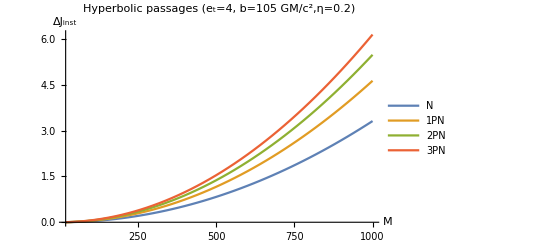

```mathematica
plot3=Plot[{JFluxN/.rel,JFlux1/.rel,JFlux2/.rel,JFlux/.rel},{M,20 ,1000 },PlotLegends->{"N","1PN","2PN","3PN"},PlotLabel->Style[Framed["Hyperbolic  passages (e_t=4, b=105 GM/c^2,η=0.2)"],8,Red,Background->Lighter[Cyan]],AxesLabel->{M,Subscript[ΔJ, inst]}]
```

```mathematica
Export["mj105.jpg",plot3,ImageResolution->300]
```

mj105.jpg

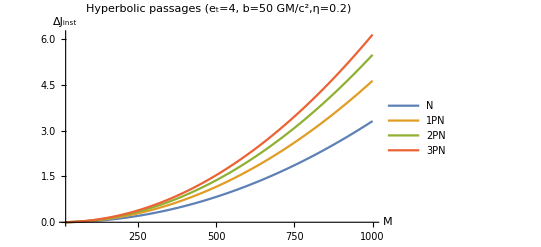

```mathematica
plot4=Plot[{JFluxN/.rel,JFlux1/.rel,JFlux2/.rel,JFlux/.rel},{M,20 ,1000 },PlotLegends->{"N","1PN","2PN","3PN"},PlotLabel->Style[Framed["Hyperbolic  passages (e_t=4, b=50 GM/c^2,η=0.2)"],8,Red,Background->Lighter[Cyan]],AxesLabel->{M,Subscript[ΔJ, inst]}]
```

```mathematica
Export["mj50.jpg",plot4,ImageResolution->300]
```

mj50.jpg